```mathematica
S =1;
τ =1;
Decay[t_]:=S ⅇ^(-t/τ)
Thermal[a_,n_,t_]:=S a/(a+t^n)
Limit[Const a/(a+t^n),t->Infinity, Assumptions->{a>0,n>0,Const>0}]
```

0

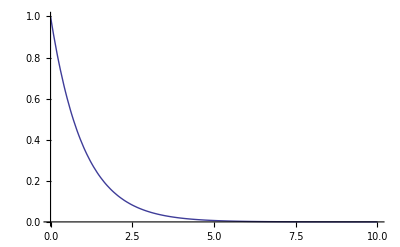

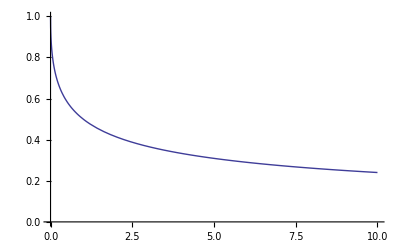
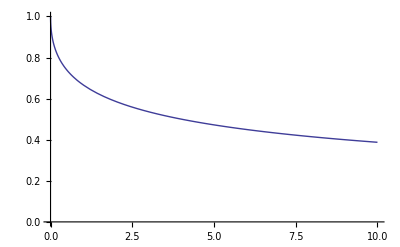
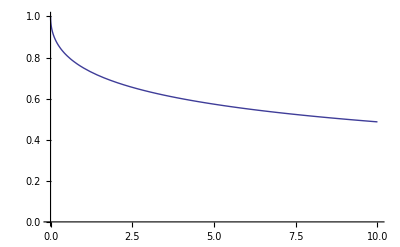
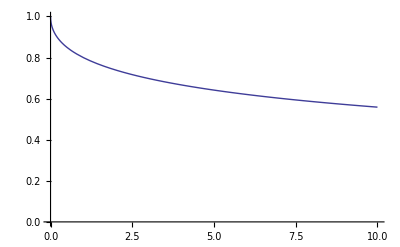
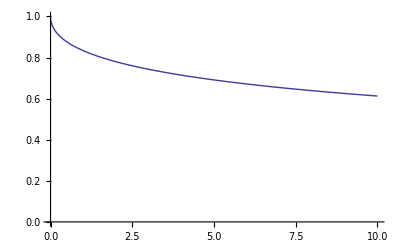
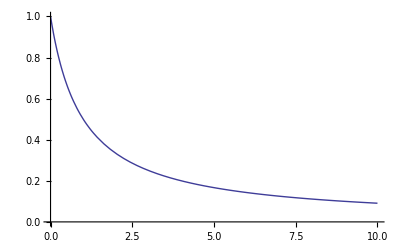
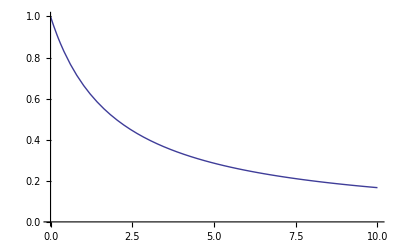

```mathematica
Plot[Decay[t],{t,0,10},PlotRange->Full]
Table[Plot[Thermal[a,n,t],{t,0,10},PlotRange->Full,AxesOrigin->{0,0}],{n,0.5,2,0.5},{a,1,5}]
```